# Notes (MATH152, 2017-09-25)

## Section 7.7: Approximate Integration

```mathematica
∫_a^b f(x)ⅆx≈(Δx/2)[f(Subscript[x, 0])+2f(Subscript[x, 1])+2f(Subscript[x, 2])+…+2f(Subscript[x, n-1])+f(Subscript[x, n])]
Δx=(b-a)/n,Subscript[x, i]=a+i Δx
```

```mathematica
∫_1^2 1/x ⅆx, n=5
(0.2/2)[1+2/1.2+2/1.4+2/1.6+2/1.8+1/2]=0.6956349206349208
```

If |f''(x)|≤K for a≤x≤b, then:

```mathematica
|Subscript[E, T]|≤(K(b-a))^3/(12 n^2), |Subscript[E, M]|≤(K(b-a))^3/(24 n^2)
```

… where E_T and E_Mare the error factor of the trapezoidal and midpoint rules, respectively.

```mathematica
Subscript[E, T]≤(2(2-1)^3)/(12 n^2)=1/(6 n^2)=1/(6·25)=1/150
```

if we want E to be ≤0.0001, for example,

```mathematica
(2(1)^3)/(12 n^2)<0.0001⟹n>1/(√0.0006)≈40.8⟹n≥41
```

```mathematica
(2(1)^3)/(24 n^2)<0.0001⟹n≥29
```

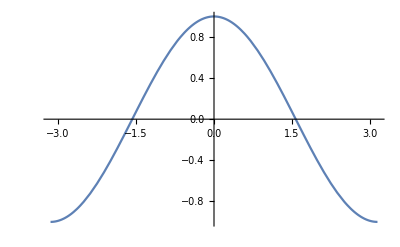

```mathematica
Plot[{Cos[x],},{x,-π,π}]
```

```mathematica
{Cos[-π],Cos[0],Cos[π]}
```

{-1,1,-1}

```mathematica
y=A x^2+B x+C
Area: ∫_-h^h A x^2+B x+Cⅆx=2∫_0^h A x^2+Cⅆx (because A x^2and C are odd, but B x is even)
=Subscript[2[A x^3/3+Subscript[C, x]], 0]^h=(h/3)[2A h^2+6C]
```

```mathematica
Subscript[y, 0]=(A(-h))^2+B(-h)+C=A h^2-B h+C
Subscript[y, 1]=C
Subscript[y, 2]=A h^2+B h+C
Subscript[y, 0]+4 Subscript[y, 1]+Subscript[y, 2]=2A h^2+6C
```

```mathematica
Area: (Subscript[y, 0]+4 Subscript[y, 1]+Subscript[y, 2])h/3
```

Thus, “Simpson’s Rule:”

```mathematica
∫_a^b f(x)ⅆx≈(Δx/3)[f(Subscript[x, 0])+4f(Subscript[x, 1])+2f(Subscript[x, 2])+4f(Subscript[x, 3])+…+4f(Subscript[x, n-1])+f(Subscript[x, n])]
Δx=(b-a)/n,n is even (to get a parabola),Subscript[x, i]=a+i Δx
```

```mathematica
∫_1^2 1/x ⅆx, n=10
(0.1/3)[1/1+4/1.1+2/1.2+4/1.3+2/1.4+4/1.5+2/1.6+4/1.7+2/1.8+4/1.9+1/2]≈0.6931502306889304
```

If |f''''(x)|≤K for a≤x≤b, then:

```mathematica
|Subscript[E, S]|≤(K(b-a))^5/(180 n^4)
```

… where E_S is the error factor of the Simpson rule.

```mathematica
Subscript[E, S]≤(2(2-1)^3)/(12 n^2)=1/(6 n^2)=1/(6·25)=1/150
```

if we want E to be ≤0.0001, for example,

```mathematica
0.0001⟹n≥6.04, n≈8
```

```mathematica
∫_0^1 ⅇ^(x^2)ⅆx, n=10
ⅆ^2/(ⅆ x^2)ⅇ^(x^2)=(2+4 x^2)ⅇ^(x^2)
ⅆ^4/(ⅆ x^4)ⅇ^(x^2)=(12+48 x^2+16 x^4)ⅇ^(x^2)
```

```mathematica
Midpoint: 0.1[e^0.0025+e^0.0225+e^0.0625+…+e^0.9025]≈1.460393
Subscript[E, M]:|f''(x)|≤6ⅇ, so Subscript[E, M]≤(6(ⅇ(1))^3)/(24(10)^2)=ⅇ/400≈0.007
1.4533≤∫_0^1 ⅇ^(x^2)ⅆx≤1.4674
```

```mathematica
Simpson: (0.1/3)[e^0+4 e^0.01+2 e^0.04+…+4 e^0.81+e^1]≈1.462681
Subscript[E, S]:0≤|f''''(x)|≤76ⅇ, so Subscript[E, S]≤(76(ⅇ(1))^5)/(180(10)^4)=(19ⅇ)/450000≈0.000115
1.4626≤∫_0^1 ⅇ^(x^2)ⅆx≤1.4628
```